## Modele epidemiologiczne

Autorzy: Paweł Polak, Jacek Strzałkowski

### Wstęp teoretyczny

Istnieje wiele modeli opisujących możliwy przebieg epidemii, różniące się pewnymi warunkami początkowymi oraz pewnymi charakterystycznymi założeniami dla każdego z modeli. W tej pracy skupimy się na dwóch podstawowych modelach jakimi są modele SIS oraz SIR. Poszczególne litery w nazwach modeli tworzą skrót słów z języka angielskiego i oznaczają kolejno : S-Susceptible, I-Infectious, R-Recovered. Modele te opierają się na obserwacji rozwoju epidemii w środowisku jakiejś grupy, gdzie rozwój epidemii jest definiowany za pomocą statusu poszczególnych członków grupy. Statusy pochodzą od podanych wcześniej skrótów i oznaczają one kolejno: S - dana osoba ma status osoby nie zarażonej, ale potencjalnie podatnej na zarażenie  I-dana osoba ma status osoby zarażonej R- oznacza osobę która nie jest zarażona, która przeszła przez chorobę, przez co albo nabrała permanentnej odporności lub umarła, więc nie bierze udziału już czynnego udziału w epidemii. Jak widać w modelu SIS, nie występuje stan R, więc jest to model przedstawiający epidemię, gdzie potencjalni zarażeni nie nabierają nigdy odporności na chorobę.

W niniejszej pracy skupiliśmy się na modelu synchronicznym i asynchronicznym dla modeli SIS i SIR. Model synchroniczny opiera się na algorytmie, gdzie dana osoba może zarazić się od swojego sąsiada dopiero w następnej ,,turze" symulacji, zaś w modelu asynchronicznym dana osoba może zarazić się w danej turze od osoby, która sama zaraziła się w tej samej turze. Warunkiem koniecznym do rozpoczęcia symulacji jest występowanie choć jednej osoby zarażonej. Przez parametr σ będziemy oznaczać początkową liczbę zakażonych . Model SIR można opisać za pomocą równań różniczkowych:

dS/dt=(β S I)/N
dI/dt=(β S I)/□N-γ I
dR/dt=γ I
gdzie S, I, R to reprezentuje grupę osób o statusach kolejno S, I oraz R, zaś N=S+I+R jest to suma wszystkich tych osób. β to współczynnik prawdopodobieństwa przejścia ze stanu S do stanu I od jednego sąsiada ze stanem I, zaś γ to współczynnik prawdopodobieństwa przejścia ze stanu I do stanu R. W modelu SIS mamy do czynienia z nieco zmodyfikowanym modelem, gdzie R=0 i γ=0 (bo osoby nie nabywają odporności w tym modelu).

Podsumowując,

S: liczba zdrowych, zdolnych do bycia zakażonymi.
I: liczba zainfekowanych
R: liczba zmarłych/ wyleczonych/ usuniętych z populacji. 
Każdy członek S może zostać zarażony z prawdpodobieństwem β przez swojego sąsiada.
Każdy zainfekowany I, może przejść do R zgodnie z prawdopodobieństwem γ.

#### Kalkulator SIR

W tej pracy będziemy korzystali z kalkulatora modelu SIR dostępnego na stronie https://www.wolframalpha.com/input/?i=sir+model dla modelu SIR oraz https://www.wolframalpha.com/input/?i=sis+model dla modelu SIS. Przykładowe dane wejściowe.

-Graphics-

Dane wejściowe kalkulatora interpretujemy następująco:

transmission rate by day  - β

recovery rate by day - γ

total population - N

initial infected population - I(t=0)=σ N

initial susceptible population S(t=0)=(1-σ)N

initial recovered population - R(t=0)=0

time - czas symulacji (w kodzie będzie oznaczany przez nTur).

#### Kalkulator SIS

-Graphics-

Recovery rate by day - α

## Metodologia

Symulacja będzie przebiegać na kwadratowej tablicy o wymiarze N. Kolorem zielonym będą zaznaczeni S, czerwonym I, i niebieskim R.
Symulacje będą się odbywać zgodnie z dwoma alternatywnymi algorytmami: synchronicznym i asynchroniczny. W modelu synchronicznym będziemy zapisywali stan tablicy po każdej turze czasowej. W modelu asynchronicznym - po sprocedowaniu każdego pola tablicy stanów (każdego członka populacji). Przez stan tablicy, rozumiemy macierz n×n, gdzie n^2=N taką, że ∀_(x∈n×n)x∈{S,I,R}. Przeprowadzone zostaną dwie symulacje: dla modelu SIR i modelu SIS w dwóch algorytmach: synchronicznym i asynchronicznym.

W następnej części  dokonamy analizy jakościowej i ilościowej relacji między  S(t), I(t), R(t) od parametrów β i γ dla modelu SIR w algorytmie synchronicznym. Wykorzystaliśmy w tym celu inny algorytm niż  w poprzednich badaniach. Pozwala on na szybsze wykonanie zadania.

## Program

W tej sekcji zaimplementowaliśmy funkcję służące do przeprowadzania symulacji, zapisywania oraz wczytywania danych. W celu wygenerowania danych do symulacji, prosimy o wczytanie danych, co można dokonać kompilując funkcje w podsekcji „Wczytywanie danych”.

### Zapis do pliku

```mathematica
SetDirectory[NotebookDirectory[]<>"/dane/"];
```

```mathematica
DumpSave["danePandemiaSynSIR.mx",{daneSynAll}]
```

```mathematica
DumpSave["danePandemiaSynSIS.mx",{daneSisSynAll}]
```

DumpSave::noopen: Cannot open dane/danePandemiaSynSIS.mx.

```mathematica
DumpSave["daneBetaST.mx",{pomiary}];
```

```mathematica
DumpSave["daneASir.mx",{daneASirAll}]
```

{{1}}
 |  |  |  |

```mathematica
DumpSave["daneASIS.mx",{daneASISAll}]
```

{1}
 |  |  |  |

### Wczytywanie danych

W celu uruchomienia symulacji, trzeba wykonać poniższe polecenia (Shift+Enter lub Enter na klawiaturze numerycznej).

```mathematica
SetDirectory[NotebookDirectory[]<>"/dane/"];
<<danePandemiaSynSIR.mx
<<danePandemiaSynSIS.mx
<<daneBetaST.mx
<<daneASir.mx
<<daneASIS.mx
```

/home/jacek/MEGAsync/uczelnia/5-semestr/lab/epidemia/dane

#### Funkcje do symulacji

Funkcja ma przyjąć tablicę NxN, której elementy mogą przyjmować trzy rodzaje wartość S, I i R, i narysować diagram. Użyjemy funkcji MatrixPlot

```mathematica
wyk[mat_]:=MatrixPlot[mat,ColorRules->{s->Green,i->Red,r->Blue},PlotLegends->Automatic]
```

Zwraca daną komórkę o ile jej adres nie przekracza zakresu wymiarów tablicy.

```mathematica
takeElement[bTab_,x_,y_]:=
If[x<1∨x>n∨y<1∨y>n,Null,bTab[[x,y]]]
```

Zwraca liczbę zakażonych sąsiadów.

```mathematica
ileSomsiadow[bTab_,x_,y_]:=
Count[{
takeElement[bTab,x-1,y-1],
takeElement[bTab,x,y-1],
takeElement[bTab,x+1,y-1],
takeElement[bTab,x-1,y],
takeElement[bTab,x+1,y],
takeElement[bTab,x-1,y+1],
takeElement[bTab,x,y+1],
takeElement[bTab,x+1,y+1]
},i]
```

#### Wykres uśredniony S̄(t), Ī(t), R̄(t)

```mathematica
ClearAll[wykresMeanSIR,wykresMeanSIS];
wykresMeanSIR[tablica_,nTur_,nSym_,tytul_:"SIR Synchroniczny"]:=
DiscretePlot[{
Mean@Table[Count[tablica[[ns,x]],s,2],{ns,nSym}],
Mean@Table[Count[tablica[[ns,x]],i,2],{ns,nSym}],
Mean@Table[Count[tablica[[ns,x]],r,2],{ns,nSym}]}
,{x,1,nTur},PlotTheme->"Scientific",PlotLabel->tytul,FrameLabel->{"czas","ilość"},Filling->None,PlotLegends->{"S","I","R"}];
wykresMeanSIS[tablica_,nTur_,nSym_,tytul_:"SIS Synchroniczny"]:=
DiscretePlot[{
Mean@Table[Count[tablica[[ns,x]],s,2],{ns,nSym}],
Mean@Table[Count[tablica[[ns,x]],i,2],{ns,nSym}]}
,{x,1,nTur},PlotTheme->"Scientific",PlotLabel->tytul,FrameLabel->{"czas","ilość"},Filling->None,PlotLegends->{"S","I"}];
```

### Algorytm synchroniczny,

W tej sekcji przedstawione są: kod źródłowy, wykres uśredniony oraz animacja przebiegu symulacji dla obu modelów.

#### SIR

Inicjalizacja. Parametry symulacji

```mathematica
β=0.05;
γ=0.03;
n=100;
σ=0.01;
nTur=250;
nSym=5;
```

```mathematica
ClearAll[daneSyn]
```

Główna pętla programu. Podczas iteracji może wystąpić zdarzenie przejścia z S→I lub I→R. Prawdopodobieństwo przejścia I→R wynosi γ. Prawdopodobieństwo zakażenia się od jednego ze swoich r chorych sąsiadów (znajdujących się w stanie I) wynosi 1-(1-β^r)

Generowanie nowych danych dla modelu SIR wg algorytmu synchronicznego. (Wykonanie programu może trochę zająć).

```mathematica
ClearAll[daneSynAll];
daneSynAll={};
Do[
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n];
daneSyn={tab};
curTab=tab;
Do[
{
oldTab=curTab;
Do[{liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤γ∧oldTab[[x,y]]==i,curTab[[x,y]]=r,]
}
,{x,1,n},{y,1,n}];
AppendTo[daneSyn,curTab];}
,nTur];
AppendTo[daneSynAll,daneSyn];
,nSym]
```

Animacja wykorzystująca zdefiniowaną wcześniej funkcję wyk[].

Animacja

```mathematica
Animate[wyk[daneSynAll[[ns,u]]],{u,1,nTur,1},{ns,1,nSym,1},AnimationRunning->False]
```

Wykres średniego (kilka symulacji) przebiegu symulacji.

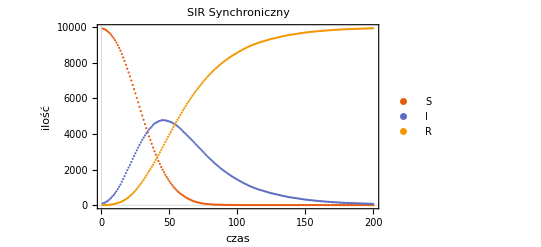

```mathematica
wykresMeanSIR[daneSynAll,nTur,nSym]
```

Kalkulator

```mathematica
initialInfectedPopulationSIR=σ*n^2
initialPopulation=n^2
time=nTur
```

100.

10000

250

Wyniki (stan na ostatnią turę).

-Graphics-

Wykres z kalkulatora (Proszę zwrócić uwagę na legendę - inne kolory oznaczają S(t), I(t) i R(t)). Na czerwono oznaczono 250 turę co odpowiada naszemu nTur.

-Graphics-

#### SIS

Wykorzystamy model SIS: β - oznacza p. S→ I, α - p. I→ S czyli wyzdrowienia

Inicjalizacja

```mathematica
β=0.05;
α=0.02;
n=100;
σ=0.01;
nTur=60;
nSym=6;
```

Pętla

```mathematica
daneSisSynAll={};
Do[
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n];
daneSisSyn={tab};
curTab=tab;
Do[
{
oldTab=curTab;
Do[{ liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤α∧curTab[[x,y]]==i,curTab[[x,y]]=s,]
}
,{x,1,n},{y,1,n}];
AppendTo[daneSisSyn,curTab]}
,nTur]
AppendTo[daneSisSynAll,daneSisSyn];
,nSym]
```

Animacja

```mathematica
Animate[wyk[daneSisSynAll[[ns,t]]],{ns,1,nSym,1},{t,1,nTur,1},AnimationRunning->False]
```

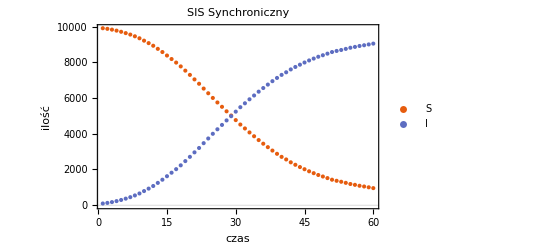

```mathematica
wykresMeanSIS[daneSisSynAll,nTur,nSym]
```

Kalkulator. Dane wejściowe

```mathematica
initialInfectedPopulationSIS=σ*n^2
```

100.

-Graphics-

Równania

-Graphics-

Wyniki

-Graphics-

-Graphics-

## Model asynchroniczny

Pętla będzie iterowana tak samo jak w modelu chronicznym. Inaczej będziemy zapisywać wartości do zmiennej zbierającej dane eksperymentu. Będzie ona aktualizowana po sprawdzeniu każdego elementu macierzy.

#### Model SIR

Inicjalizacja

```mathematica
β=0.05;
γ=0.03;
σ=0.01;
n=30;
nTur=50;
nSym=6;
```

Pętla programu

```mathematica
daneASirAll={};
Do[
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n];
daneASir={tab};
curTab=tab;
Do[
{
oldTab=curTab;
Do[{liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤γ∧oldTab[[x,y]]==i,curTab[[x,y]]=r,],
AppendTo[daneASir,curTab];
}
,{x,1,n},{y,1,n}];
}
,nTur];
AppendTo[daneASirAll,daneASir];
,nSym]
```

Animacja

```mathematica
Animate[wyk[daneASirAll[[numerSymulacji,t]]],{t,1,nTur*n^2,1},{numerSymulacji,1,nSym,1},AnimationRunning->False]
```

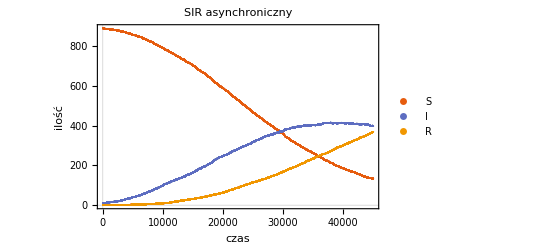

```mathematica
wykresMeanSIR[daneASirAll,nTur*n^2,nSym,"SIR asynchroniczny"] (* Oś x - to nie jest czas jako tura czasowa, ale numer tury *)
```

Kalkulator

-Graphics-

-Graphics-

-Graphics-

#### SIS

Inicjalizacja

```mathematica
β=0.05;
α=0.02;
n=20;
σ=0.01;
nTur=100;
nSym=2;
```

Pętla

```mathematica
daneASISAll={};
Do[
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n];
daneASIS={tab};
curTab=tab;
Do[
{
oldTab=curTab;
Do[{ liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤α∧curTab[[x,y]]==i,curTab[[x,y]]=s,],
AppendTo[daneASIS,curTab]
}
,{x,1,n},{y,1,n}];
}
,nTur]
AppendTo[daneASISAll,daneASIS];
,nSym]
```

Animacja

```mathematica
Animate[wyk[daneASISAll[[numerSymulacji,t]]],{t,1,nTur*n^2,1},{numerSymulacji,1,nSym,1},AnimationRunning->False]
```

Wykres

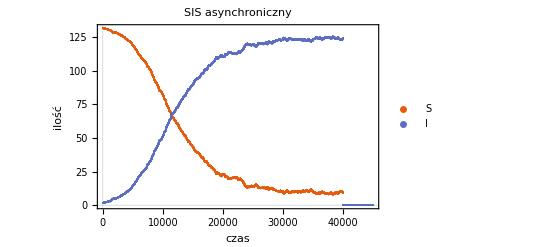

```mathematica
wykresMeanSIS[daneASISAll,nTur*n^2,nSym,"SIS asynchroniczny"] (* Oś x - to nie jest czas jako tura czasowa, ale numer tury *)
```

-Graphics-

-Graphics-

-Graphics-

## Zależność przebiegu symulacji od parametrów β i γ

Sprawdzimy w jaki sposób zmieniają się przebiegi funkcji S(t_k)(β),I(t_k)(β),R(t_k)(β) i S(t_k)(γ),I(t_k)(γ),R(t_k)(γ), gdzie t_k - końcowa chwila symulacji.

## Zależność od β

Główna pętla programu. Podczas iteracji może wystąpić zdarzenie przejścia z S→I lub I→R. Prawdopodobieństwo przejścia I→R wynosi γ. Prawdopodobieństwo zakażenia się od jednego ze swoich r chorych sąsiadów (znajdujących się w stanie I) wynosi 1-(1-β)^r dla r - liczba sąsiadów.  Zmieniając parametr β będziemy zmieniać więc przebieg symulacji.

Wybrane parametry (poza β, która będzie zmieniana w trakcie)

```mathematica
γ=0.05;
n=100;
σ=0.02;
nTur=300;
begPar=0.01;
endPar=0.02;
dPar=0.001;
```

Kod symulacji. Zmieniliśmy algorytm, ponieważ poprzedni uniemożliwiał przeprowadzenie symulacji dla odpowiednio dużej liczby tur.

```mathematica
nSym=IntegerPart[(endPar-begPar)/dPar+1];
pomiary=Table[{0,0,0,0},{i,nSym}];
For[β=begPar,β≤endPar,β+=dPar,
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n]; (* Pierwsza tablica *)
nSasiad=Table[0,{i,n},{j,n}];
	For[x=1,x≤Dimensions[tab][[1]],x++,For[y=1,y≤Dimensions[tab][[2]],y++,
	If[tab[[x,y]]==i,
{
If[x<n∧y<n,nSasiad[[x+1,y+1]]+=1,],
If[x<n,nSasiad[[x+1,y]]+=1,],
If[x<n∧y>1,nSasiad[[x+1,y-1]]+=1,],
If[y>1n,nSasiad[[x,y+1]]+=1,],
If[y<n,nSasiad[[x,y-1]]+=1,],
If[x>1∧y<n,nSasiad[[x-1,y+1]]+=1,],
If[x>1,nSasiad[[x-1,y]]+=1,],
If[x>1∧y>1,nSasiad[[x-1,y-1]]+=1,]}
,]
]];
daneSyn={tab};
curTab=tab;
iS=IntegerPart[(β-begPar)/dPar +1];(* Numer pomiaru β*)
pomiary[[iS,1]]=β;
pomiary[[iS,2]]=γ;
Do[
{oldTab=curTab;
Do[
(*{liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤γ∧oldTab[[x,y]]==i,curTab[[x,y]]=r,]
}
*){cnS=nSasiad[[x,y]],
Switch[curTab[[x,y]],
s,If[cnS>0∧RandomReal[]≤1-(1-β)^cnS,
{curTab[[x,y]]=i,
If[x<n∧y<n,nSasiad[[x+1,y+1]]+=1,],
If[x<n,nSasiad[[x+1,y]]+=1,],
If[x<n∧y>1,nSasiad[[x+1,y-1]]+=1,],
If[y>1n,nSasiad[[x,y+1]]+=1,],
If[y<n,nSasiad[[x,y-1]]+=1,],
If[x>1∧y<n,nSasiad[[x-1,y+1]]+=1,],
If[x>1,nSasiad[[x-1,y]]+=1,],
If[x>1∧y>1,nSasiad[[x-1,y-1]]+=1,]}
,],
i,If[RandomReal[]≤γ∧oldTab[[x,y]]==i,
{curTab[[x,y]]=r,
If[x<n∧y<n,nSasiad[[x+1,y+1]]-=1,],
If[x<n,nSasiad[[x+1,y]]-=1,],
If[x<n∧y>1,nSasiad[[x+1,y-1]]-=1,],
If[y>1n,nSasiad[[x,y+1]]-=1,],
If[y<n,nSasiad[[x,y-1]]-=1,],
If[x>1∧y<n,nSasiad[[x-1,y+1]]-=1,],
If[x>1,nSasiad[[x-1,y]]-=1,],
If[x>1∧y>1,nSasiad[[x-1,y-1]]-=1,]}
,]
]}

,{x,1,n},{y,1,n}];
AppendTo[daneSyn,curTab];}
,nTur];
pomiary[[iS,3]]=Count[daneSyn[[nTur]],s,2];
pomiary[[iS,4]]=Count[daneSyn[[nTur]],r,2];
]
```

```mathematica
pomiaryβ=pomiary
```

{{0.011,0.05,8472,1527},{0,0,0,0},{0.012,0.05,8202,1790},{0.013,0.05,7475,2515},{0.014,0.05,7207,2771},{0.015,0.05,6425,3570},{0.016,0.05,5709,4273},{0.017,0.05,5319,4656},{0.018,0.05,4937,5049},{0.019,0.05,3386,6576},{0.02,0.05,3034,6950}}

Wykres zależności przebiegu czasowego populacji od parametru β. (Pomarańczowy S(t_k), niebieski R(t_k))

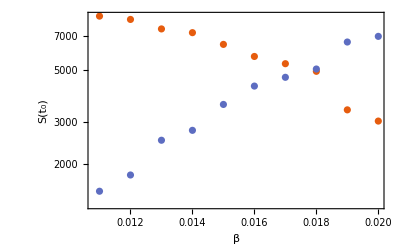

```mathematica
ListLogPlot[{{pomiaryᵀ[[1]],pomiaryᵀ[[3]]}ᵀ,{pomiaryᵀ[[1]],pomiaryᵀ[[4]]}ᵀ}
,PlotTheme->"Scientific",FrameLabel->{"β","S(t_0)"}]
```

## Zależność od γ

```mathematica
β=0.02;
n=100;
σ=0.02;
nTur=300;
begPar=0.01;
endPar=0.02;
dPar=0.001;
```

```mathematica
nSym=IntegerPart[(endPar-begPar)/dPar+1];
pomiary=Table[{0,0,0,0},{i,nSym}];
For[γ=begPar,γ≤endPar,γ+=dPar,
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n]; (* Pierwsza tablica *)
nSasiad=Table[0,{i,n},{j,n}];
	For[x=1,x≤Dimensions[tab][[1]],x++,For[y=1,y≤Dimensions[tab][[2]],y++,
	If[tab[[x,y]]==i,
{
If[x<n∧y<n,nSasiad[[x+1,y+1]]+=1,],
If[x<n,nSasiad[[x+1,y]]+=1,],
If[x<n∧y>1,nSasiad[[x+1,y-1]]+=1,],
If[y>1n,nSasiad[[x,y+1]]+=1,],
If[y<n,nSasiad[[x,y-1]]+=1,],
If[x>1∧y<n,nSasiad[[x-1,y+1]]+=1,],
If[x>1,nSasiad[[x-1,y]]+=1,],
If[x>1∧y>1,nSasiad[[x-1,y-1]]+=1,]}
,]
]];
daneSyn={tab};
curTab=tab;
iS=IntegerPart[(γ-begPar)/dPar +1];(* Numer pomiaru β*)
pomiary[[iS,1]]=β;
pomiary[[iS,2]]=γ;
Do[
{oldTab=curTab;
Do[
(*{liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤γ∧oldTab[[x,y]]==i,curTab[[x,y]]=r,]
}
*){cnS=nSasiad[[x,y]],
Switch[curTab[[x,y]],
s,If[cnS>0∧RandomReal[]≤1-(1-β)^cnS,
{curTab[[x,y]]=i,
If[x<n∧y<n,nSasiad[[x+1,y+1]]+=1,],
If[x<n,nSasiad[[x+1,y]]+=1,],
If[x<n∧y>1,nSasiad[[x+1,y-1]]+=1,],
If[y>1n,nSasiad[[x,y+1]]+=1,],
If[y<n,nSasiad[[x,y-1]]+=1,],
If[x>1∧y<n,nSasiad[[x-1,y+1]]+=1,],
If[x>1,nSasiad[[x-1,y]]+=1,],
If[x>1∧y>1,nSasiad[[x-1,y-1]]+=1,]}
,],
i,If[RandomReal[]≤γ∧oldTab[[x,y]]==i,
{curTab[[x,y]]=r,
If[x<n∧y<n,nSasiad[[x+1,y+1]]-=1,],
If[x<n,nSasiad[[x+1,y]]-=1,],
If[x<n∧y>1,nSasiad[[x+1,y-1]]-=1,],
If[y>1n,nSasiad[[x,y+1]]-=1,],
If[y<n,nSasiad[[x,y-1]]-=1,],
If[x>1∧y<n,nSasiad[[x-1,y+1]]-=1,],
If[x>1,nSasiad[[x-1,y]]-=1,],
If[x>1∧y>1,nSasiad[[x-1,y-1]]-=1,]}
,]
]}

,{x,1,n},{y,1,n}];
AppendTo[daneSyn,curTab];}
,nTur];
pomiary[[iS,3]]=Count[daneSyn[[nTur]],s,2];
pomiary[[iS,4]]=Count[daneSyn[[nTur]],r,2];
]
```

```mathematica
pomiaryγ=pomiary
```

{{0.02,0.01,5,9095},{0.02,0.02,134,9765},{0.02,0.03,525,9436},{0.02,0.04,2286,7659},{0.02,0.05,3342,6557},{0.02,0.06,6121,3877},{0.02,0.07,7024,2968},{0.02,0.08,8068,1932},{0.02,0.09,8557,1443},{0.02,0.1,8850,1150}}

Wykres zależności przebiegu czasowego populacji od parametru γ.

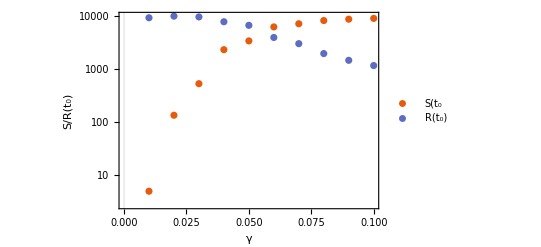

../fig/gamma.pdf

```mathematica
ListLogPlot[{{pomiaryᵀ[[2]],pomiaryᵀ[[3]]}ᵀ,{pomiaryᵀ[[2]],pomiaryᵀ[[4]]}ᵀ}
,PlotTheme->"Scientific",FrameLabel->{"γ","S/R(t_0)"},PlotLegends->{"S(t_0","R(t_0)"}]
Export["../fig/gamma.pdf",%]
```

Wykres zależności przebiegu czasowego populacji od parametru γ dla mniejszego zakresu γ∈(0.01,0.02) .

```mathematica
pomiaryγ2=pomiary
```

{{0.02,0.011,9,9308},{0,0,0,0},{0.02,0.012,18,9407},{0.02,0.013,27,9540},{0.02,0.014,42,9577},{0.02,0.015,45,9607},{0.02,0.016,41,9723},{0.02,0.017,72,9736},{0.02,0.018,103,9678},{0.02,0.019,134,9714},{0.02,0.02,131,9727}}

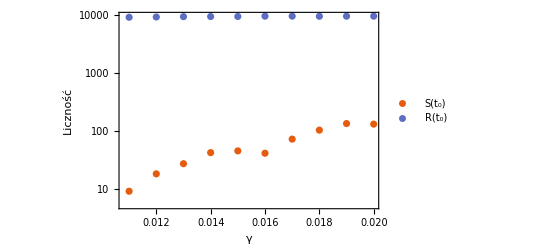

../fig/gamma2.pdf

```mathematica
ListLogPlot[{{pomiaryᵀ[[2]],pomiaryᵀ[[3]]}ᵀ,{pomiaryᵀ[[2]],pomiaryᵀ[[4]]}ᵀ}
,PlotTheme->"Scientific",FrameLabel->{"γ","Liczność"},PlotLegends->{"S(t_0)","R(t_0)"}]
Export["../fig/gamma2.pdf",%]
```

### Podsumowanie

W niniejszej pracy przedstawiliśmy charakterystyki czasowe populacji w różnych modelach epidemiologicznych. Porównanie uzyskanych w wyniku symulacji danych wraz z informacjami uzyskanymi z kalkulatora świadczą, że nasz model zjawiska oraz ten z kalkulatora nie są tożsame. Przyczyny tego mogą być następujące (...).

Porównanie wpływu parametrów β i γ na charakterystykę czasową daje następujące wnioski: β∝R(t_k), β∝S^-1(t_k). Przyczyną takiego stanu rzeczy możę być (....). Wraz ze wzrostem γ maleje S(t_k) oraz maleje R(t_k) . Interpretujemy to następująco: im większe γ, tym więcej osób zdąży wyzdrowieć, nim populacja się zakończy.